# Analytical approximations closed as desired to special functions

## Approximations and Plots Restoration

## Bessel K_2

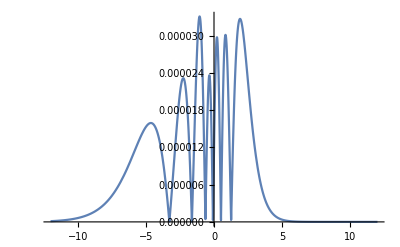

```mathematica
k2App[x_,c0_]:=Exp[-x]*SetPrecision[(1+2.627/x+2/x^2)/((0.033*x^(c0/5)-0.102*x^(c0/4)+0.113*x^(c0/3)+1.162*x^(c0/2)+(2*x/π)^c0+1)^(1/(2c0))),100]
ϵ[x_]:=Abs[1-k2App[x,1.984]/BesselK[2,x]]
Plot[ϵ[SetPrecision[10^logx,100]],{logx,-12,12},PlotRange->All]
```

## Synchrotron function

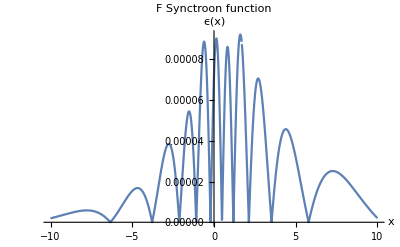

```mathematica
δ = 30;
Fapp[x_]:=ⅇ^-x SetPrecision[(230/107*x^(1/3)+x-0.7078*x^0.701)/((2.835*x^0.61264-0.967*x^0.3792-0.701*x^0.8239-0.61264*x^0.89696+((2x)/π)^1.1843+1)^0.42219),100]
smallF[x_]:=x NIntegrate[ BesselK[5/3,t],{t,x,∞},AccuracyGoal->15,WorkingPrecision->15,MinRecursion->5,MaxRecursion->20]
expansion=Simplify[y∫_y^∞ Normal[Series[BesselK[5/3,t],{t,∞,10}]]ⅆt,Assumptions->y>0];
largeF[x_]:=expansion/.y->x;

F[x_]:=If[x<50,
smallF[x],
largeF[x]
]
Fapp[x_]:=SetPrecision[ⅇ^-x,δ]SetPrecision[(230/107*x^(1/3)+x-0.7078*x^0.701)/((2.835*x^0.61264-0.967*x^0.3792-0.701*x^0.8239-0.61264*x^0.89696+((2x)/π)^1.1843+1)^0.42219),δ]
ϵ[x_]:=Abs[1-Fapp[x]/F[x]]
Plot[ϵ[SetPrecision[10^logx,δ]],{logx,-10,10},PlotRange->All,PlotLabel->"F Synctroon function",AxesLabel->{"x","ϵ(x)"}]
```

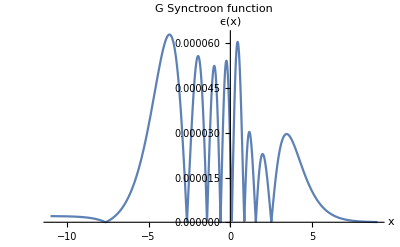

```mathematica
G[x_]:=x BesselK[2/3,x]
Gapp[x_]:=ⅇ^-x SetPrecision[ (115/107 x^(1/3)+x)/((3.96 x^0.6366+4.815 x^1.425+1.74 x^2.1711+((2 x)/π)^(54/19)+1)^(19/108)),δ]
ϵ[x_]:=Abs[1-Gapp[x]/G[x]]
Plot[Abs[ϵ[SetPrecision[10^logx,δ]]],{logx,-11,9},PlotRange->All,PlotLabel->"G Synctroon function",AxesLabel->{"x","ϵ(x)"}]
```

## Polylog

```mathematica
constantsMatrix=({{5, -1.2, 0.49, 663, -227, 3.371, 139, -10.5, 46, 236, 9.7, 286, -10, -1.66}, {7.7, -0.67, 0.057, 473, -23, 3.376, 58, -7.4, -212, 241, 9, 312, -11, -1.24}, {11.8, -1.1, 0.09, 519, 28, 3.58, 57, -5.2, -547, 255, 7.9, 346, -12.7, -1.13}, {1.4732, 0.125, 0.00198, 5.4, 12.1, 1.02, 10.84, 4.37, 13, 135.1, 11.79, 404, -10.8, -1.885}, {1.52, 0.0964, 0.0011, 15.35, 28.15, 1.1931, 20, 6.596, -94.5, 131.8, 11.86, 443.67, -11.46, -2.152}, {3.02, 0.196, 0.0093, 37.8, 57.3, 0.9295, 33.17, 8.74, 50.6, 116, 12, 476, -11.8, -1.283}, {24, -0.17, 0.128, 100.8, 132, 0.5685, 63.5, 13.14, 300, 88.6, 11.6, 541, -13, -0.775}, {32.2, 38.7, 38.8, 9.75, 22.3, 1.206, 13, 6.82, 103.6, 71.7, 10, 651, -15.3, 0.12638}, {26.569, 26.69, 15.88, 34.7, 62.38, 0.253, 27.33, 10.18, 633.79, 30.8, 7.64, 681.3, -17.2, 0.25076}, {42.95, 36.9, 12.34, 85.5, 122.17, 1.197, 49.79, 12.114, 516.26, 19.4, 5.8, 768.2, -20.8, 0.3759}, {103.84, 92.24, 19.97, 26.76, 17.39, 7.02, 13.8, 3.58, -164, 33, 5.4, 1050, -27, 0.50028}, {9.774, 2.909, 0, 235, 326, 0.091, 126.2, 15.65, 715.8, -16.4, 2.6, 711.8, -28, 1.25}, {70.4, 60.6, 8.25, 1855, 836, 3, 179, 14.3, 202, -19, 1, 229, -24.6, 0.7488}, {149, 76.3, 4.63, 1012, 887, -34.2, 284, 28.3, 342, -29.9, 1.36, 206, -18.8, 0.8758}, {233.98, 112.86, 7.98, 10.3, 11, -1, 7, 1.81, 2004, -24, 2.8, 1981, -30, 1.00017}, {280.6, 122.3, 5.132, 22, 20, -82, 9, 22.7, 809, -48, 1.3, 629, -39, 1.124}});
f[x_,s_,cRow_]:=Module[{},
{c0,c1,c2,c3,c4,c5,c6,c7,c8,c9,c10,c11,c12,c13}=constantsMatrix[[cRow]];
-1/Gamma[s] 1/(2Cosh[2x]+((c8+c9*x^2+c10*x^4)/(c11+c12*x^2+x^4/c10)))(Gamma[s]*ⅇ^-x-c5 ⅇ^x+1/s*Exp[2*x]*(c3+c4*x^2+c6*x^4+c7*x^6+x^8)^(s/8)+Exp[2*x]*(c0+c1*x^2+c2*x^4)^c13)
];


xvalues=Join[-Reverse[#],#]&@Table[10^x,{x,-2,2,.000001}];
sValues={1/3,1/2,2/3,4/3,3/2,5/3,2,5/2,3,7/2,4,9/2,5,11/2,6,13/2};
ϵ[x_,s_,cRow_]:=Abs[1-Re[PolyLog[SetPrecision[s,50],-ⅇ^SetPrecision[x,50]]]/f[x,s,cRow]]
ϵs=ParallelTable[{i,sValues[[i]],SetPrecision[Max[ϵ[#,sValues[[i]],i]&/@xvalues],2]},{i,Length[sValues]}];
Grid[Prepend[ϵs,{"Index","s Value","Max Abs relative Difference"}],Frame->All]
```

Index | s Value | Max Abs relative Difference
1 | 1/3 | 0.00046
2 | 1/2 | 0.00059
3 | 2/3 | 0.00065
4 | 4/3 | 0.000069
5 | 3/2 | 0.00004
6 | 5/3 | 0.000058
7 | 2 | 0.000047
8 | 5/2 | 0.000048
9 | 3 | 0.000025
10 | 7/2 | 0.000036
11 | 4 | 0.000046
12 | 9/2 | 0.000064
13 | 5 | 0.0002
14 | 11/2 | 0.00014
15 | 6 | 0.000048
16 | 13/2 | 0.00012

## Fermi gas pressure

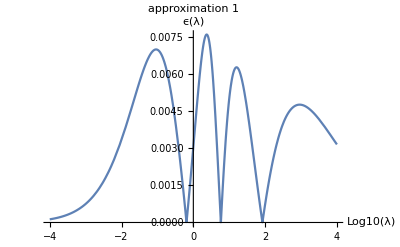

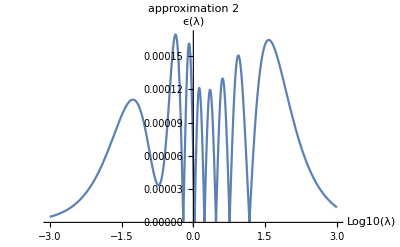

```mathematica
δ=400;
Idist[λ_]:=NIntegrate[((x^2-1)^(3/2))/(ⅇ^SetPrecision[ λ x,δ]+1),{x,1,∞},WorkingPrecision->δ,MaxRecursion->30,AccuracyGoal->35]
fTilde1[λ_]:=Exp[-λ]*SetPrecision[(111.3/λ^3.05-108/λ^3.045+(3*Sqrt[2*π])/(2*λ^2.5)+(7*π^4)/(120*λ^4)),100]
fTilde2[λ_]:=Exp[-λ]*SetPrecision[Sqrt[(9*π*λ^8/2+47.95*λ^7+95.3*λ^6+55*λ^5+102.6*λ^4-12*λ^3+37*λ^2+81.1*λ+49*π^8/14400)/(λ^5-0.33*λ^4+2.18*λ^3-1.597*λ^2+0.522*λ+1)]/λ^4,100]
ϵ1[λ_]:=Abs[1-fTilde1[λ]/Idist[λ]]
ϵ2[λ_]:=Abs[1-fTilde2[λ]/Idist[λ]]

Plot[ϵ1[SetPrecision[10^logx,100]],{logx,-4,4},PlotRange->All,PlotLabel->"approximation 1",AxesLabel->{"Log10(λ)","ϵ(λ)"}]
Plot[ϵ2[SetPrecision[10^logx,100]],{logx,-3,3},PlotRange->All,PlotLabel->"approximation 2",AxesLabel->{"Log10(λ)","ϵ(λ)"}]
```

## Fermi&Bose gas pressure

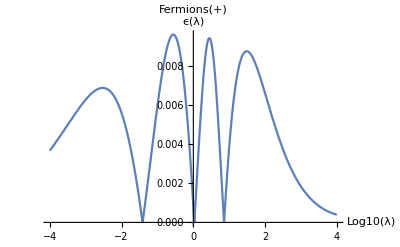

```mathematica
δ=400;
Idist[λ_,α_]:=NIntegrate[((x^2-1)^(3/2))/(ⅇ^SetPrecision[ λ x,δ]+α),{x,1,∞},WorkingPrecision->δ,MaxRecursion->30,AccuracyGoal->35]
ITilde[λ_,α_]:=Exp[-λ]*SetPrecision[(3*Sqrt[2*π]/(2*λ^2.5)+(π^4*(15-α))/(16*15*λ^4)-(1+α/5)/λ^3.6+(22/5+α*3/20)/λ^(10/3)),100]

ϵ[λ_,α_]:=Abs[1-ITilde[λ,α]/Idist[λ,α]]
Plot[ϵ[SetPrecision[10^logx,100],1],{logx,-4,4},PlotRange->All,PlotLabel->"Fermions(+)",AxesLabel->{"Log10(λ)","ϵ(λ)"}]
Plot[ϵ[SetPrecision[10^logx,100],-1],{logx,-4,4},PlotRange->All,PlotLabel->"Bosons(+)",AxesLabel->{"Log10(λ)","ϵ(λ)"}]
```

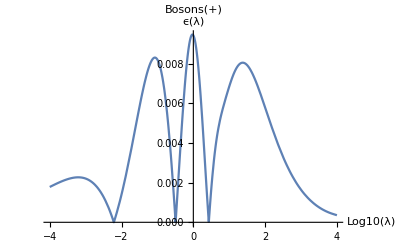

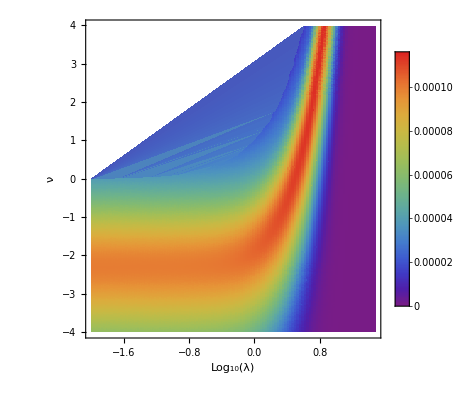

```mathematica
calc[λ_,ν_]:=1/λ^2(3 ⅇ^ν BesselK[2,λ]-0.8857 ⅇ^(2.0411 ν) BesselK[2,2.0411 λ]+1.0814 ⅇ^(2.787 ν) BesselK[2,2.787 λ]-0.7283 ⅇ^(2.92 ν) BesselK[2,2.92 λ]);
δ=30;
NI[λ_,ν_]:=If[ν≤λ,NIntegrate[(t^2-1)^(3/2)/(E^(SetPrecision[λ t-ν,δ])+1),{t,1,∞},AccuracyGoal->δ,MaxRecursion->22,WorkingPrecision->δ],NaN];
values=Flatten[Table[{λ,ν,
1-NI[10^λ,ν]/calc[10^λ,ν]},{λ,-2,1.5,.03},{ν,-4,4,.03}],1];
ListDensityPlot[values,ColorFunction->"Rainbow",PlotLegends->Automatic,FrameLabel->{"Log_10(λ)","ν"},PlotRange->All]
```

## 1/(1+ⅇ^x)

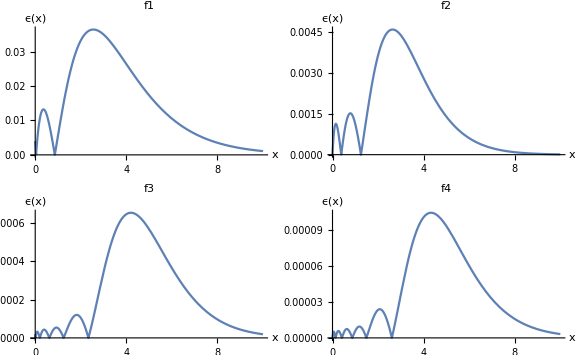

```mathematica
real[x_]:=1/(1+ⅇ^x);
f1[x_]:=-0.502*Exp[-1.609*x]+Exp[-x]
f2[x_]:=2.5*Exp[-2.172*x]-3*Exp[-2.057*x]+Exp[-x]
f3[x_]:=-3.836*Exp[-2.7392*x]+5.1041*Exp[-2.6425*x]-1.76811*Exp[-2.11001*x]+Exp[-x]
f4[x_]:=0.60323*Exp[-3.75592*x]-2.30875*Exp[-3.3734*x]+2.2573*Exp[-3.052*x]-1.05178*Exp[-2.01231*x]+Exp[-x]
ϵ[x_,n_]:=Abs[1-({f1,f2,f3,f4}[[n]][x])/real[x]]
plot1=Plot[ϵ[x,1],{x,0,10},PlotRange->All,PlotLabel->"f1",AxesLabel->{"x","ϵ(x)"}];
plot2=Plot[ϵ[x,2],{x,0,10},PlotRange->All,PlotLabel->"f2",AxesLabel->{"x","ϵ(x)"}];
plot3=Plot[ϵ[x,3],{x,0,10},PlotRange->All,PlotLabel->"f3",AxesLabel->{"x","ϵ(x)"}];
plot4=Plot[ϵ[x,4],{x,0,10},PlotRange->All,PlotLabel->"f4",AxesLabel->{"x","ϵ(x)"}];
GraphicsGrid[{{plot1,plot2},{plot3,plot4}},ImageSize->Large]
```

```mathematica
calc=1/λ^2(3 ⅇ^ν BesselK[2,λ]-0.8857 ⅇ^(2.0411 ν) BesselK[2,2.0411 λ]+1.0814 ⅇ^(2.787 ν) BesselK[2,2.787 λ]-0.7283 ⅇ^(2.92 ν) BesselK[2,2.92 λ]);
calc/.{λ->10,ν->5}
tildeI[5,0]/Idist[5,0]
```

0.0000956725

1.00007

```mathematica
NI[λ_,ν_]:=NI[λ,ν]=If[ν≤λ,NIntegrate[(t^2-1)^(3/2)/(E^(λ t-ν)+1),{t,1,∞},AccuracyGoal->420,MaxRecursion->22],NaN];
```

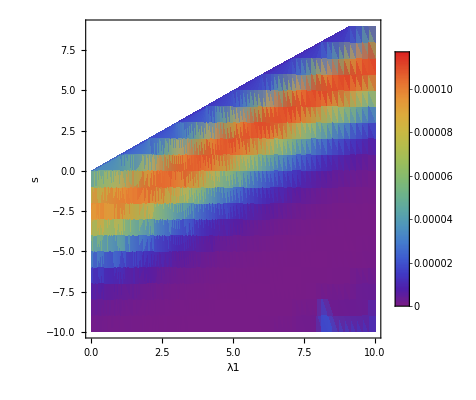

```mathematica
NI[λ_,ν_]:=If[ν<λ,NIntegrate[(t^2-1)^(3/2)/(ⅇ^(λ t-ν)+ 1),{t,1,∞},{AccuracyGoal->12,MaxRecursion->22}],Nand];
calc[λ_,ν_]:=1/λ^2(3 ⅇ^ν BesselK[2,λ]-0.8857 ⅇ^(2.0411 ν) BesselK[2,2.0411 λ]+1.0814 ⅇ^(2.787 ν) BesselK[2,2.787 λ]-0.7283 ⅇ^(2.92 ν) BesselK[2,2.92 λ]);
values=Flatten[ParallelTable[{10^log10λ,ν,
1-NI[10^log10λ,ν]/calc[10^log10λ,ν]},{log10λ,-2,1,.01},{ν,-10,50,1}],1];
plot=ListDensityPlot[values,ColorFunction->"Rainbow",PlotLegends->Automatic,AxesLabel->{"λ1","s"},PlotRange->All]
Export["IBessels.png",plot];
```

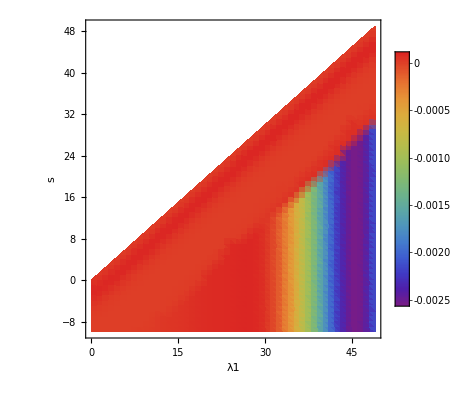

```mathematica
NI[λ_,ν_]:=If[ν<λ,NIntegrate[(t^2-1)^(3/2)/(ⅇ^(λ t-ν)+ 1),{t,1,∞},{AccuracyGoal->12,MaxRecursion->22}],Nand];
calc[λ_,ν_]:=1/λ^2(3 ⅇ^ν BesselK[2,λ]-0.8857 ⅇ^(2.0411 ν) BesselK[2,2.0411 λ]+1.0814 ⅇ^(2.787 ν) BesselK[2,2.787 λ]-0.7283 ⅇ^(2.92 ν) BesselK[2,2.92 λ]);
values=Flatten[Table[{λ,ν,
1-NI[λ,ν]/calc[λ,ν]},{λ,0.001,50,1},{ν,-10,50,1}],1];
plot=ListDensityPlot[values,ColorFunction->"Rainbow",PlotLegends->Automatic,AxesLabel->{"λ1","s"},PlotRange->All]
Export["IBessels.png",plot];
```

```mathematica
NI[λ_,ν_]:=If[ν<λ,NIntegrate[(t^2-1)^(3/2)/(ⅇ^SetPrecision[λ t-ν,100]+ 1),{t,1,∞},{AccuracyGoal->12,MaxRecursion->22,WorkingPrecision->100}],Nand];
calc[λ_,ν_]:=1/λ^2(3 ⅇ^ν BesselK[2,λ]-0.8857 ⅇ^(2.0411 ν) BesselK[2,2.0411 λ]+1.0814 ⅇ^(2.787 ν) BesselK[2,2.787 λ]-0.7283 ⅇ^(2.92 ν) BesselK[2,2.92 λ]);
values=Flatten[Table[{λ,ν,
1-NI[λ,ν]/calc[λ,ν]},{λ,10^-5,50,.1},{ν,-10,50,.1}],1];
plot=ListDensityPlot[values,ColorFunction->"Rainbow",PlotLegends->Automatic,AxesLabel->{"λ1","s"},PlotRange->All]
Export["IBessels.png",plot];
```

-Graphics-

```mathematica
(0.3028/(√(4π)))^2
```

0.00729629

## Error function

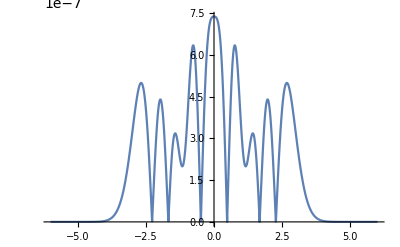

```mathematica
erfApprox[x_]:=Tanh[1.12838 x (0.007 x^6+0.09126 x^4+0.38336 x^2+1)/(0.00162 x^6+0.06485 x^4+0.29228 x^2+1)]
Plot[Abs[1-erfApprox[x]/Erf[x]],{x,-6,6}]
```

## Fermi&Bose gas number density

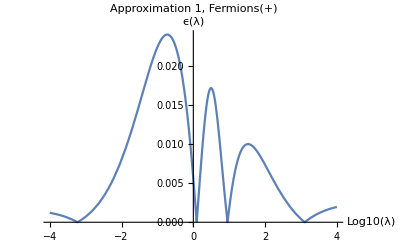

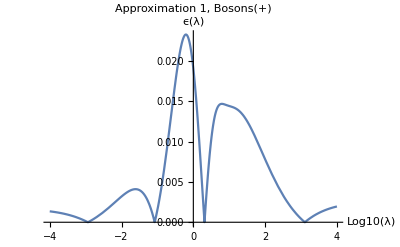

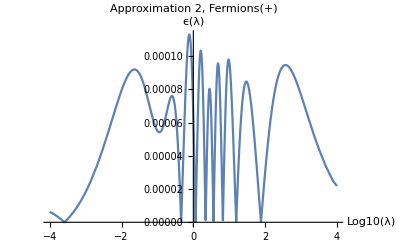

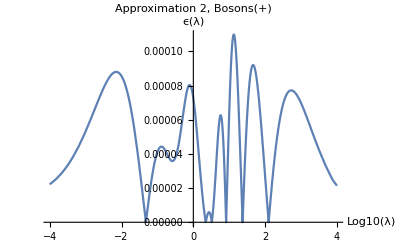

```mathematica
δ=400;
Idist[λ_,α_]:=NIntegrate[x^2/(ⅇ^(√SetPrecision[ x^2+λ^2,δ])+α),{x,0,∞},WorkingPrecision->δ,MaxRecursion->30,AccuracyGoal->35]
ITilde1[λ_,α_]:=Exp[-λ]*SetPrecision[(-3/10*(α-7)+12/11*λ^(3/4)+5/4*λ^(3/2)),100]
ITilde2[λ_,α_]:=Exp[-λ]*SetPrecision[Sqrt[π/2] λ^(3/2)+(58/193) (7-α)+(1+α+0.155 λ^3+1.232 λ+λ^(0.587-α*0.365) (-1.024*α-0.135)-λ^(2.21-α*0.313) (0.1343+α*0.0834))/(0.0831 λ^(2.464)+0.81 λ^(-α*0.886-0.148)+1),100]
ϵ1[λ_,α_]:=Abs[1-ITilde1[λ,α]/Idist[λ,α]]
ϵ2[λ_,α_]:=Abs[1-ITilde2[λ,α]/Idist[λ,α]]
Plot[ϵ1[SetPrecision[10^logx,100],1],{logx,-4,4},PlotRange->All,PlotLabel->"Approximation 1, Fermions(+)",AxesLabel->{"Log10(λ)","ϵ(λ)"}]
Plot[ϵ1[SetPrecision[10^logx,100],-1],{logx,-4,4},PlotRange->All,PlotLabel->"Approximation 1, Bosons(+)",AxesLabel->{"Log10(λ)","ϵ(λ)"}]

Plot[ϵ2[SetPrecision[10^logx,100],1],{logx,-4,4},PlotRange->All,PlotLabel->"Approximation 2, Fermions(+)",AxesLabel->{"Log10(λ)","ϵ(λ)"}]
Plot[ϵ2[SetPrecision[10^logx,100],-1],{logx,-4,4},PlotRange->All,PlotLabel->"Approximation 2, Bosons(+)",AxesLabel->{"Log10(λ)","ϵ(λ)"}]
```